```mathematica
SetDirectory[NotebookDirectory[]]
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]*)
(*SetDirectory["build-converterUNV-Desktop-u041eu0442u043bu0430u0434u043au0430"]*)
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug"}]]*)
```

/home/v.korchagova/Документы/BMSTU/RKDG2D

```mathematica
mesh=Import["Mesh2D","Table"];
```

```mathematica
(*nodes*)
offset=2;
nNodes=mesh[[offset,1]]
nodes=Table[mesh[[i]],{i,offset+1,nNodes+offset}]
(*edges*)
offset=3+nNodes+1+1;
nEdgesBoundary=mesh[[offset,1]]
nEdges=mesh[[offset+1,1]]
edges=Table[mesh[[i]],{i,offset+2,nEdges+offset+1}]
(*cells*)
offset = offset +nEdges+4;
nCells=mesh[[offset]][[1]]
cells=Table[mesh[[i]],{i,offset+1,nCells+offset}]
(*cell centers*)
offset = offset +nCells+4;
cellCenters=Table[mesh[[i]],{i,offset,nCells+offset-1}]
(*adjoint cells for edges*)
offset = nCells+offset+5;
edgeAdj=Table[mesh[[i]],{i,offset,nEdges+offset-3}]

(*edge normals*)
offset = nEdges+offset+1;
edgeNormals=Table[mesh[[i]],{i,offset,nEdges+offset-1}]
```

113

{{-0.5,-0.5},{-0.5,0.5},{0.5,-0.5},{0.5,0.5},{0.25,-6.12323×10^-17},{-0.5,-0.375},{-0.5,-0.25},{-0.5,-0.125},{-0.5,0},{-0.5,0.125},{-0.5,0.25},{-0.5,0.375},{-0.375,-0.5},{-0.25,-0.5},{-0.125,-0.5},{0,-0.5},{0.125,-0.5},{0.25,-0.5},{0.375,-0.5},{-0.375,0.5},{-0.25,0.5},{-0.125,0.5},{0,0.5},{0.125,0.5},{0.25,0.5},{0.375,0.5},{0.5,-0.375},{0.5,-0.25},{0.5,-0.125},{0.5,0},{0.5,0.125},{0.5,0.25},{0.5,0.375},{0.216506,0.125},{0.125,0.216506},{1.53081×10^-17,0.25},{-0.125,0.216506},{-0.216506,0.125},{-0.25,1.41638×10^-16},{-0.216506,-0.125},{-0.125,-0.216506},{-4.59243×10^-17,-0.25},{0.125,-0.216506},{0.216506,-0.125},{-0.331909,-0.099915},{0.312757,-0.0873258},{0.000725419,0.450715},{-0.156573,-0.349198},{0.168646,-0.33875},{0.204601,0.233277},{-0.204441,0.233249},{0.31779,0.415032},{-0.317723,0.415087},{0.452017,0.194361},{0.452849,-0.341227},{-0.452013,0.194364},{-0.45623,-0.326758},{0.427228,0.43228},{0.186228,0.412666},{-0.185486,0.413178},{-0.427214,0.432292},{0.391945,0.0599614},{0.446935,-0.069594},{0.400937,-0.207303},{0.232241,-0.235587},{0.320808,-0.384257},{0.421436,-0.408562},{0.178975,-0.438561},{0.0880661,-0.423259},{-0.391677,0.0609899},{-0.427609,-0.0876064},{-0.239403,-0.218503},{-0.400252,-0.18839},{-0.315371,-0.387067},{-0.0598967,-0.456737},{-0.202128,-0.427577},{-0.419846,-0.430247},{-0.009052,-0.402598},{-0.301603,0.213683},{-0.411346,0.342419},{-0.244544,0.322307},{-0.0644445,0.379888},{0.301629,0.21367},{0.0672172,0.378991},{0.244766,0.322255},{0.411367,0.3424},{-0.0993624,-0.410347},{0.236753,-0.395241},{0.385069,-0.0340491},{0.317728,-0.268587},{-0.38284,-0.0248082},{0.397835,-0.312016},{0.256544,-0.318949},{-0.315524,-0.263615},{-0.311402,0.111514},{0.311438,0.111388},{-0.416442,-0.366094},{-0.398729,0.245575},{0.398742,0.245562},{0.0537324,-0.325483},{-0.0548345,-0.324231},{0.392549,-0.116479},{0.308678,-0.174306},{-0.22733,-0.379032},{0.393355,0.153829},{-0.393319,0.153949},{-0.400191,-0.293716},{-0.305808,-0.178129},{-0.138467,0.303531},{0.139224,0.303491},{-0.335533,0.311018},{0.33558,0.310982},{-0.223534,-0.308574}}

44

295

{{1,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,2},{1,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,3},{2,20},{20,21},{21,22},{22,23},{23,24},{24,25},{25,26},{26,4},{3,27},{27,28},{28,29},{29,30},{30,31},{31,32},{32,33},{33,4},{5,34},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,42},{42,43},{43,44},{44,5},{58,33},{4,58},{86,58},{58,52},{52,86},{26,58},{85,52},{52,59},{59,85},{24,59},{59,25},{47,84},{84,24},{24,47},{25,52},{52,26},{21,60},{60,22},{60,82},{82,22},{47,23},{22,47},{81,60},{60,53},{53,81},{20,53},{53,21},{80,53},{53,61},{61,80},{61,20},{2,61},{62,30},{31,62},{54,105},{105,31},{31,54},{102,103},{103,64},{64,102},{62,89},{89,30},{32,54},{90,92},{92,64},{64,90},{88,93},{93,49},{49,88},{71,45},{45,91},{91,71},{27,67},{67,3},{67,19},{69,68},{68,49},{49,69},{69,17},{17,68},{19,66},{66,18},{18,68},{46,102},{102,89},{89,46},{67,66},{55,92},{92,67},{67,55},{66,88},{88,18},{27,55},{65,90},{90,103},{103,65},{92,28},{28,64},{28,55},{30,63},{63,29},{29,64},{63,102},{102,29},{92,66},{70,106},{106,10},{10,70},{8,71},{71,9},{9,70},{91,9},{60,109},{109,82},{94,74},{74,113},{113,94},{97,74},{74,107},{107,97},{38,79},{79,95},{95,38},{15,87},{87,76},{76,15},{77,97},{97,6},{6,77},{75,87},{15,75},{76,14},{16,75},{1,77},{104,48},{48,113},{113,104},{13,77},{14,74},{74,13},{72,94},{113,72},{56,106},{106,98},{98,56},{76,74},{99,86},{86,112},{112,99},{105,62},{77,74},{85,83},{83,112},{112,85},{53,111},{111,81},{98,79},{79,111},{111,98},{59,110},{110,85},{57,7},{6,57},{35,50},{50,110},{110,35},{36,109},{109,37},{81,51},{51,109},{109,81},{71,73},{73,45},{73,8},{7,73},{72,40},{40,108},{108,72},{57,107},{107,7},{108,45},{73,108},{94,73},{73,107},{107,94},{57,97},{56,10},{79,106},{106,95},{96,62},{105,96},{54,99},{99,105},{90,93},{93,66},{66,90},{69,78},{78,16},{16,69},{76,48},{104,76},{49,100},{100,69},{75,78},{78,87},{104,74},{46,44},{44,103},{103,46},{113,41},{41,72},{40,45},{41,101},{101,42},{65,44},{43,65},{42,100},{100,43},{49,65},{43,49},{78,100},{100,101},{101,78},{46,5},{48,87},{87,101},{101,48},{63,89},{48,41},{32,99},{95,39},{51,79},{38,51},{70,95},{80,11},{11,98},{98,80},{79,81},{80,12},{56,11},{51,37},{61,12},{82,47},{80,111},{83,105},{99,83},{52,112},{96,5},{5,62},{83,96},{83,50},{50,34},{34,83},{68,88},{84,59},{84,110},{96,34},{32,86},{70,39},{33,86},{85,50},{82,84},{110,36},{94,108},{65,93},{84,36},{82,36},{89,5},{91,70},{45,39},{39,91}}

182

{{45,32,46},{47,48,49},{46,24,50},{51,52,53},{54,55,22},{56,57,58},{59,60,23},{61,62,19},{63,64,62},{65,20,66},{67,68,69},{70,71,18},{72,73,74},{75,17,76},{58,21,65},{77,29,78},{79,80,81},{82,83,84},{85,86,77},{87,81,30},{88,89,90},{91,92,93},{94,95,96},{25,97,98},{98,99,16},{100,101,102},{100,103,104},{15,105,106},{104,14,107},{108,109,110},{111,105,99},{112,113,114},{115,116,106},{114,97,117},{118,119,120},{89,121,122},{117,26,123},{124,125,28},{122,27,126},{127,128,125},{111,113,129},{130,131,132},{133,134,4},{132,5,135},{96,136,134},{63,137,138},{139,140,141},{142,143,144},{145,146,147},{148,149,150},{151,152,153},{154,148,155},{156,11,150},{157,155,12},{153,1,158},{159,160,161},{162,158,9},{10,163,164},{165,141,166},{167,168,169},{170,163,156},{171,172,173},{78,80,174},{151,175,142},{176,177,178},{69,179,180},{181,182,183},{53,184,185},{186,2,187},{188,189,190},{36,191,192},{193,194,195},{196,197,94},{198,3,199},{200,201,202},{203,204,186},{205,197,206},{207,208,209},{210,144,203},{196,133,198},{211,131,167},{146,212,213},{214,174,215},{216,217,79},{218,219,220},{221,222,223},{224,159,225},{103,223,13},{226,227,102},{154,228,229},{170,225,230},{231,232,233},{166,234,235},{90,83,119},{126,128,84},{205,201,236},{235,40,200},{233,82,108},{41,237,238},{239,43,240},{241,242,42},{243,240,244},{245,246,247},{248,44,231},{244,242,226},{120,232,239},{221,227,245},{249,250,251},{252,109,127},{247,250,229},{253,234,160},{251,237,253},{87,254,216},{199,204,208},{147,255,38},{256,145,257},{258,213,130},{259,260,261},{180,182,262},{263,7,259},{211,264,6},{169,260,264},{75,73,70},{192,194,265},{164,175,162},{74,266,263},{76,8,266},{71,68,61},{66,64,267},{195,137,67},{268,179,72},{256,193,262},{269,217,270},{49,271,172},{214,272,273},{215,269,274},{275,276,277},{187,152,210},{101,278,93},{222,228,157},{261,183,268},{54,57,279},{55,52,59},{280,184,279},{60,48,50},{33,272,281},{171,254,282},{277,281,274},{283,255,258},{178,271,51},{282,31,284},{181,168,212},{47,284,45},{238,246,241},{275,176,285},{173,177,270},{286,56,267},{209,143,139},{161,140,230},{185,189,285},{190,287,35},{207,288,206},{118,289,218},{290,287,280},{286,291,290},{138,191,291},{115,219,91},{220,129,88},{123,121,112},{110,292,248},{135,136,293},{294,295,95},{265,257,37},{243,92,289},{202,288,165},{236,39,294},{293,295,283},{224,149,249},{273,292,85},{124,86,252},{276,188,34},{107,116,278}}

{{0.475743,0.43576},{0.385462,0.396571},{0.434076,0.477427},{0.249595,0.383318},{0.187076,0.470889},{0.0643142,0.443236},{0.314263,0.471677},{-0.186829,0.471059},{-0.124977,0.431022},{-0.0414249,0.483572},{-0.249251,0.383524},{-0.314241,0.471696},{-0.385428,0.396599},{-0.434071,0.477431},{0.0419085,0.483572},{0.463982,0.0616538},{0.448457,0.15773},{0.367388,-0.166029},{0.425671,0.00863743},{0.484006,0.189787},{0.372167,-0.262636},{0.220648,-0.35098},{-0.380786,-0.0707765},{0.473812,-0.427854},{0.432145,-0.469521},{0.145229,-0.40019},{0.13068,-0.45394},{0.315269,-0.461419},{0.184658,-0.47952},{0.363458,-0.0792847},{0.372415,-0.43094},{0.42404,-0.353935},{0.269187,-0.426499},{0.458095,-0.37493},{0.286216,-0.22616},{0.432924,-0.25644},{0.484283,-0.322076},{0.482312,-0.0648647},{0.466979,-0.194101},{0.446495,-0.103691},{0.380026,-0.368278},{-0.428332,0.113313},{-0.47587,-0.0708688},{-0.463892,0.0619966},{-0.436816,-0.0374715},{-0.129466,0.365532},{-0.28481,-0.319752},{-0.377334,-0.348959},{-0.276504,0.150066},{-0.142163,-0.445975},{-0.445429,-0.390447},{-0.0947531,-0.455695},{-0.192376,-0.475859},{-0.0616322,-0.485579},{-0.473282,-0.435082},{-0.202479,-0.345602},{-0.431615,-0.476749},{-0.313457,-0.462356},{-0.259487,-0.263564},{-0.414687,0.197963},{-0.255833,-0.438215},{0.381896,0.299648},{0.428433,0.11293},{-0.383886,-0.394469},{0.293992,0.282302},{-0.299267,0.349471},{-0.345288,0.256759},{0.190073,0.346137},{-0.48541,-0.317253},{0.156275,0.251091},{-0.0878225,0.256679},{-0.195818,0.286362},{-0.38659,-0.125304},{-0.466751,-0.187797},{-0.253906,-0.173877},{-0.45214,-0.290158},{-0.34599,-0.155478},{-0.371989,-0.248574},{-0.424287,-0.328856},{-0.44262,-0.133665},{-0.448444,0.157771},{-0.335441,0.159715},{0.365579,0.108393},{0.414705,0.197917},{0.29836,-0.323931},{0.026338,-0.441952},{-0.195344,-0.385269},{0.071022,-0.47442},{0.103481,-0.362497},{-0.0561037,-0.423227},{-0.248276,-0.397892},{0.279314,-0.128877},{-0.195979,-0.247861},{0.342448,-0.216732},{0.431162,-0.149594},{-0.284741,-0.134348},{-0.193637,-0.18667},{0.337995,-0.126037},{-0.0599448,-0.263579},{0.191249,-0.192364},{0.0595775,-0.263996},{0.175296,-0.263614},{-0.0033847,-0.350771},{0.259754,-0.0707753},{0.115793,-0.29358},{0.252475,-0.178298},{0.0442488,-0.38378},{-0.10359,-0.361259},{0.408184,-0.0733741},{-0.0544163,-0.379059},{-0.168369,-0.291426},{-0.112136,-0.296645},{0.450253,0.229974},{-0.433481,-0.244035},{-0.259303,0.0788382},{-0.24085,0.190644},{-0.365466,0.108818},{-0.436692,0.279332},{-0.293893,0.282336},{-0.470449,0.322473},{-0.484004,0.189788},{-0.450247,0.22998},{-0.373313,0.449126},{-0.15597,0.251095},{-0.370072,-0.439105},{-0.446187,0.383237},{-0.475738,0.435764},{-0.25107,0.442755},{-0.0629063,0.443534},{-0.189499,0.346339},{-0.354867,0.356175},{-0.250196,0.256413},{0.364575,0.204354},{0.354912,0.356138},{0.317794,0.0571164},{0.335474,0.159629},{0.240912,0.190649},{-0.457557,-0.35595},{0.194791,-0.390851},{-0.0229829,-0.453112},{-0.381869,0.299671},{0.126148,0.430553},{0.25134,0.442566},{0.13089,0.36505},{0.373339,0.449104},{0.259315,0.078796},{0.436703,0.279321},{0.276524,0.150019},{-0.317693,0.0575015},{0.299379,0.349423},{0.470456,0.322467},{-0.364551,0.204402},{0.446198,0.383227},{-0.00036737,-0.299905},{0.250332,0.256401},{0.345317,0.256738},{0.00116604,0.403198},{-0.343695,-0.3148},{-0.255412,-0.358224},{0.196197,0.286341},{0.0880746,0.256666},{-0.340528,-0.210045},{0.268838,-0.274375},{0.0688137,0.310827},{0.000924238,0.336293},{-0.0676373,0.31114},{0.271369,-0.366149},{0.345457,-0.32162},{0.450228,-0.301081},{0.315942,-0.0404583},{-0.424839,0.0120606},{-0.321583,-0.0415744},{-0.181983,0.191585},{0.219144,-0.297762},{-0.286912,-0.220083},{-0.266139,-0.0749717},{-0.341506,0.0120606},{-0.152688,-0.395707},{0.342338,0.00863743},{0.444001,-0.0345477},{0.182036,0.191594},{0.221909,-0.444601}}

{{74},{43},{44},{121},{120},{127},{57},{58},{53},{54},{88},{29},{28},{25},{14},{12},{8},{10},{15},{5},{7},{3},{24},{37},{39},{38},{16},{20},{151},{1},{146},{181},{161},{71},{173},{115},{176},{97},{99},{101},{100},{104},{1,153},{1,3},{2,153},{2,145},{2,134},{3,145},{4,150},{4,143},{4,68},{5,142},{5,143},{6,157},{6,142},{6,15},{7,143},{7,145},{8,128},{8,9},{9,46},{9,129},{10,15},{10,129},{11,130},{11,128},{11,66},{12,123},{12,128},{13,131},{13,123},{13,126},{14,123},{14,127},{16,19},{16,63},{17,84},{17,63},{17,20},{18,98},{18,94},{18,95},{19,179},{19,180},{20,113},{21,168},{21,36},{21,94},{22,167},{22,174},{22,139},{23,73},{23,172},{23,45},{24,34},{24,25},{25,31},{26,27},{26,139},{26,89},{27,88},{27,29},{28,31},{28,33},{29,182},{30,98},{30,109},{30,170},{31,41},{32,169},{32,41},{32,34},{33,167},{33,182},{34,37},{35,163},{35,94},{35,106},{36,169},{36,39},{37,169},{38,180},{38,40},{39,95},{40,109},{40,95},{41,168},{42,117},{42,81},{42,44},{43,80},{43,45},{44,171},{45,171},{46,130},{46,166},{47,158},{47,159},{47,59},{48,64},{48,158},{48,79},{49,116},{49,82},{49,115},{50,52},{50,178},{50,53},{51,64},{51,138},{51,55},{52,90},{52,54},{53,61},{54,140},{55,57},{56,87},{56,111},{56,159},{57,125},{58,61},{58,125},{59,175},{59,93},{60,81},{60,152},{60,122},{61,91},{62,147},{62,134},{62,156},{63,83},{64,125},{65,155},{65,156},{65,150},{66,131},{66,119},{67,152},{67,119},{67,141},{68,144},{68,160},{69,76},{69,138},{70,181},{70,160},{70,161},{71,166},{71,124},{72,132},{72,124},{72,130},{73,80},{73,77},{74,80},{74,114},{75,97},{75,96},{75,175},{76,79},{76,114},{77,96},{77,162},{78,162},{78,114},{78,158},{79,138},{81,121},{82,152},{82,117},{83,135},{83,136},{84,113},{84,133},{85,163},{85,167},{85,168},{86,107},{86,140},{86,88},{87,178},{87,91},{89,105},{89,107},{90,140},{90,110},{91,159},{92,104},{92,106},{92,98},{93,111},{93,97},{96,176},{99,112},{99,154},{100,106},{100,102},{101,154},{101,105},{102,174},{102,105},{103,107},{103,154},{103,110},{104,170},{108,178},{108,110},{108,112},{109,180},{111,112},{113,147},{115,149},{116,132},{116,173},{117,149},{118,120},{118,122},{118,141},{119,132},{120,126},{121,122},{124,173},{126,127},{129,157},{131,141},{133,136},{133,156},{134,150},{135,146},{135,179},{136,148},{137,155},{137,181},{137,148},{139,182},{142,144},{144,164},{146,148},{147,151},{149,177},{151,153},{155,160},{157,165},{161,164},{162,175},{163,174},{164,165},{165,166},{170,179},{171,177},{172,176},{172,177}}

{{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{-0.965926,-0.258819},{-0.707107,-0.707107},{-0.258819,-0.965926},{0.258819,-0.965926},{0.707107,-0.707107},{0.965926,-0.258819},{0.965926,0.258819},{0.707107,0.707107},{0.258819,0.965926},{-0.258819,0.965926},{-0.707107,0.707107},{-0.965926,0.258819},{-0.618504,-0.785782},{-0.681238,0.732062},{0.984783,-0.173786},{-0.155689,0.987806},{-0.613156,-0.789962},{-0.791856,-0.610708},{0.785789,-0.618494},{-0.0179772,0.999838},{-0.839416,-0.54349},{-0.818816,-0.574057},{0.807607,-0.589721},{-0.733348,-0.679854},{0.902398,-0.430904},{-0.368649,0.929569},{-0.781694,-0.623662},{0.8295,-0.558506},{-0.802665,-0.59643},{0.820517,-0.571622},{-0.26518,-0.964199},{0.892936,0.450183},{0.999892,0.0147173},{-0.364965,-0.931021},{0.838474,-0.544942},{0.0144352,0.999896},{-0.785163,-0.619289},{-0.829029,-0.559206},{0.781798,-0.623532},{0.61315,-0.789967},{0.155229,0.987879},{-0.984768,-0.173871},{0.791885,-0.610671},{-0.681108,-0.732183},{-0.485214,-0.874395},{-0.515693,0.856773},{-0.568446,0.822721},{-0.260961,-0.965349},{0.82239,0.568924},{-0.567629,0.823284},{-0.336769,-0.941587},{0.995763,0.0919572},{-0.997336,0.0729396},{0.284055,-0.958808},{-0.757287,0.653083},{-0.476599,-0.879121},{0.999562,-0.0296075},{-0.593025,0.805184},{0.96796,-0.251103},{-0.21976,0.975554},{-0.638412,-0.769695},{-0.127566,-0.99183},{0.827651,0.561243},{-0.814267,0.58049},{-0.392851,0.919602},{-0.758481,-0.651696},{-0.891613,0.452798},{-0.165997,-0.986126},{0.994688,0.102932},{-0.723731,0.690083},{-0.901073,-0.433667},{0.751267,-0.659998},{0.905649,0.424029},{-0.853031,0.52186},{0.654219,0.756305},{-0.343174,-0.939272},{0.995908,0.0903736},{-0.593153,0.80509},{0.234791,0.972046},{0.468967,0.883216},{-0.971399,-0.237455},{0.906232,-0.422781},{-0.129576,0.99157},{-0.9921,-0.125449},{0.582308,0.812968},{-0.360129,-0.932902},{0.995425,0.095551},{-0.625514,0.780213},{0.518902,-0.854834},{0.395806,0.918334},{-0.88836,0.459148},{-0.795204,0.606342},{-0.722197,-0.691688},{-0.639042,0.769172},{-0.652951,0.757401},{-0.0790524,-0.99687},{-0.684081,0.729406},{0.999844,0.0176649},{-0.261888,0.965098},{-0.508736,-0.860923},{0.458939,-0.888468},{0.770873,0.636989},{0.490617,-0.871375},{0.207154,0.978308},{-0.919064,-0.394108},{0.717997,-0.696046},{-0.999999,-0.00124002},{0.649718,-0.760175},{0.439102,0.898437},{-0.203181,-0.979141},{0.740113,0.672482},{-0.975708,0.219075},{0.721545,0.692368},{-0.995432,0.0954718},{0.140696,-0.990053},{0.96146,-0.274944},{-0.165352,0.986235},{-0.684523,-0.728992},{0.998595,-0.0529886},{-0.105989,0.994367},{-0.567515,-0.823363},{0.761661,0.647976},{0.553466,-0.832872},{-0.834223,0.551427},{0.585528,0.810652},{0.656463,-0.754358},{0.388515,-0.921442},{0.518684,0.854966},{-0.998552,0.053798},{0.841152,0.540799},{0.865465,0.500969},{-0.884302,0.466915},{-0.509835,0.860272},{0.984832,0.173513},{-0.567129,-0.823629},{0.998262,0.0589376},{-0.692947,0.720988},{0.336826,0.941567},{0.991609,-0.129276},{-0.382945,0.923771},{-0.719415,-0.694581},{-0.999887,0.0150207},{0.381972,-0.924174},{-0.885882,-0.463911},{0.944187,-0.329411},{0.123183,0.992384},{-0.985672,0.168676},{0.123127,-0.992391},{-0.311976,-0.95009},{0.944275,0.329159},{-0.719344,0.694654},{-0.91849,0.395445},{0.175044,-0.984561},{0.868688,0.495359},{0.740601,-0.671945},{0.206159,-0.978519},{0.731865,0.681449},{-0.986893,0.161379},{0.360587,0.932726},{-0.988236,-0.152935},{-0.911819,-0.410593},{0.729098,-0.68441},{0.174298,0.984693},{-0.965079,-0.26196},{0.791388,-0.611314},{0.536359,0.84399},{0.5255,-0.850793},{0.971301,-0.237852},{-0.511294,0.859406},{-0.519512,-0.854463},{0.507899,-0.861416},{0.401203,0.915989},{0.948575,0.316552},{0.108009,-0.99415},{0.663926,0.747798},{-1,-0.000585434},{0.334982,-0.942225},{-0.703052,-0.711138},{-0.822382,0.568935},{-0.545748,0.837949},{-0.459963,-0.887938},{-0.538326,-0.842736},{-0.460024,0.887906},{0.692938,0.720997},{-0.99828,0.0586235},{-0.635521,0.772083},{-0.712778,-0.70139},{0.999646,0.0266217},{0.20808,0.978112},{-0.995709,-0.0925358},{0.656969,-0.753918},{0.864574,-0.502506},{-0.887525,-0.46076},{0.11469,0.993401},{-0.94352,-0.331315},{0.728936,-0.684582},{-0.0854918,0.996339},{-0.0908825,0.995862},{-0.364492,0.931206},{-0.471688,-0.881765},{0.998902,-0.0468401},{0.682726,-0.730674},{-0.0174506,0.999848},{0.212409,0.977181},{-0.837929,-0.54578},{0.804339,-0.59417},{0.990029,0.140866},{-0.175171,-0.984538},{-0.814672,-0.579923},{0.836922,-0.547323},{0.851251,-0.524758},{-0.941773,-0.336251},{0.775482,-0.63137},{0.0115351,0.999933},{-0.863452,-0.504431},{0.812054,0.583582},{-0.730235,-0.683196},{0.888282,-0.459299},{-0.238337,0.971182},{0.49818,0.867074},{0.97284,-0.231478},{-0.0437839,0.999041},{-0.875987,-0.482335},{-0.197416,0.98032},{0.993846,-0.110769},{0.532669,-0.846323},{-0.721657,0.692251},{-0.0436482,-0.999047},{0.99162,0.129192},{0.885295,-0.46503},{0.344947,0.938622},{0.757245,0.65313},{-0.206225,-0.978505},{-0.618507,0.78578},{0.735883,-0.677109},{-0.382664,-0.923887},{-0.546391,-0.83753},{-0.312014,0.950078},{-0.985697,-0.168526},{-0.875636,0.482971},{0.389133,-0.921182},{-0.995433,-0.0954612},{0.198076,0.980187},{-0.994009,-0.109295},{0.721388,-0.692531},{0.599882,-0.800089},{0.272266,-0.962222},{-0.723653,-0.690164},{0.141936,0.989876},{0.721661,0.692247},{-0.395404,-0.918507},{-0.345202,0.938528},{-0.911442,0.411429},{-0.00681146,-0.999977},{-0.358647,0.933473},{0.993603,-0.112925},{-0.960033,-0.279886},{-0.886818,0.462119},{-0.895801,-0.444454},{0.244439,0.969665},{0.994738,0.102453},{0.773348,-0.633982},{-0.183578,0.983005}}

```mathematica
(*patches*)
offset=offset+nEdges+2;
nPatches=mesh[[offset]][[1]]
offset = offset+1;
patchNames={};
patchEdgeGroups={};
For[i=1,i≤nPatches, ++i,
{
patchNames=Append[patchNames,mesh[[offset,1]]];
(*Print[patchNames];*)
nEdgesInPatch=mesh[[offset+1,1]];
(*Print[nEdgesInPatch];*)
patchEdgeGroups = Append[patchEdgeGroups,Table[mesh[[i,1]],{i,offset+2,offset+1+nEdgesInPatch}]];
offset=offset+2+nEdgesInPatch;
(*Print[offset];*)
}];
patchNames
```

2

{Group_1,Group_2}

```mathematica
(*drawing functions*)
```

```mathematica
drawNode[iNode_]:=Point[nodes[[iNode]]];
drawEdgeArrow[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeLine[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeNormal[iEdge_]:=Arrow[{(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2,(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2+edgeNormals[[i]]*0.25*Norm[{nodes[[edges[[iEdge,2]]]]-nodes[[edges[[iEdge,1]]]]},2]}];
drawCell[iCell_]:=
Return[{nodes[[edges[[cells[[iCell,1]],1]]]],
nodes[[edges[[cells[[iCell,1]],2]]]],
nodes[[edges[[cells[[iCell,2]],2]]]]}];
drawPatch[color_,iPatch_]:={color,Table[drawEdgeLine[patchEdgeGroups[[i,j]]],{j,1,Length[patchEdgeGroups[[i]]]}]};
```

```mathematica
(*pictures*)
```

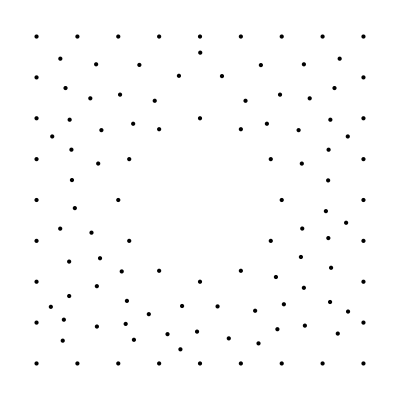

```mathematica
Graphics[Table[drawNode[i],{i,1,nNodes}]]
```

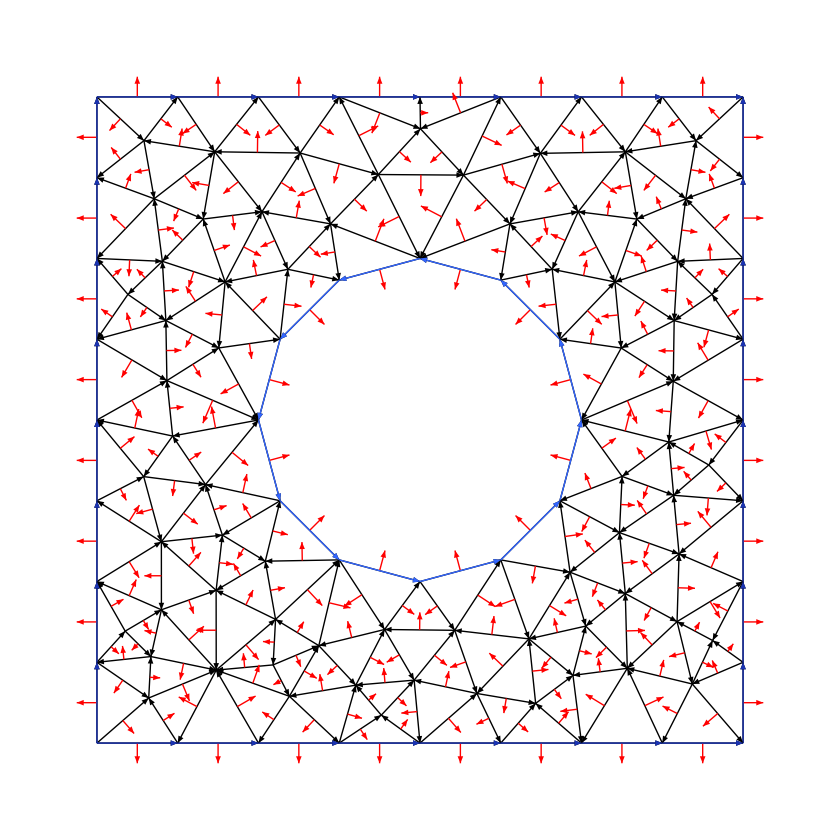

```mathematica
Graphics[{Table[drawEdgeArrow[i],{i,1,nEdges}],
Red,Arrowheads[0.02],
Table[drawEdgeNormal[i],{i,1,nEdges}],Thick,
Table[drawPatch[RGBColor[i*0.1,i*0.2,i*0.7],i],{i,1,nPatches}]}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[Directive[Thick,Black]],Cyan,
Table[Polygon[{drawCell[i]}],{i,1,p}],Black,
Table[Point[{cellCenters[[i]]}],{i,1,p}]},PlotRange->Full],{p,1,nCells}]
```